## Newton — Term 2 Exam

## Tuesday, Oct. 11

### 1. An Arc in the Evanescent Limit (a riff on a problem posed by Ben)

On the curve below, the tangent at the point (x=-1/4,y=-1) is drawn.

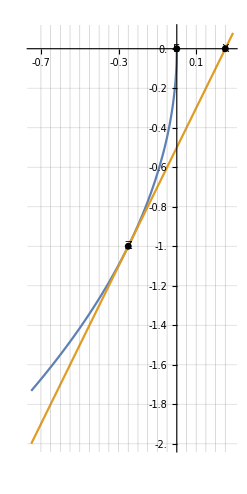

```mathematica
Plot[{-2Sqrt[-x], 2(x+1/4)-1}, {x, -0.75, 0.29}, AspectRatio->2, PlotRange->{{-0.75,0.29},{-2, 0.08}}, GridLines->{Range[-0.7, 0.25, 0.05],Range[-2.0,0.05,0.05]}, Ticks->{Range[-0.7, 0.2, 0.1], Range[-2.0, 0.0, 0.1]}, Epilog->{PointSize[0.02],
Point[{0.0,0.0}],Text["E",{0, 0},{-2,2}],
Point[{0.25,0.0}],Text["X",{0.25, 0},{-2,2}],
Point[{-0.25,-1.0}],Text["Z",{-0.25, -1.0},{-2,2}]}]
```

Assume that the centripetal force originating from S (not shown) is at a point far to the left of Z. For definiteness, let us place it at (-10.25, -1.0), so that it is 10 units of distance to the left of Z, and EX and SZ are parallel. Also assume that it is fine that anything you say when answering below is only approximate and that it is meant to become exact only in the evanescent limit where Z gets closer and closer to E.

(a) What does Lemma 6 Corollary 1 tell us about the accelerative force at Z? Answer in terms of quantities such as EX (which refers to the length of segment EX). If necessary, introduce additional points and  segments onto the drawing. An image of Lemma 6 Corollary 1 is below.

(b) The drawing is well-labeled with coordinate axes and a grid, so you can easily determine the lengths of the segments you found in (a). What does your whatever you said about the accelerative force in part (a) amount to in terms of these lengths.

(c) Consider the three-sided figure EZX. It has some area. What can you say about the ratio of the area of EZ’X’ to the area of EZX if Z’ were at (x=-1/16, y=-1/2).

-Graphics-

### 2. A Frisbee is Thrown (a merger of two distinct problems posed by Luke and by Sofia)

Prof. Hill tosses a Frisbee whose tilt is down on the left side. Viewed from above, the Frisbee follows the arc below over the course of four seconds, starting from (x=60, y=0):

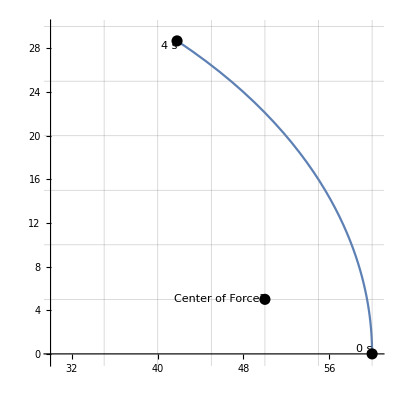

```mathematica
ParametricPlot[{60Cos[0.2 u^2], 40Sin[0.2 u^2]}, {u, 0, 2}, PlotRange->{{30, 60.5},{-0.5, 30}}, AspectRatio->1,GridLines->{Range[30, 60, 5],Range[0, 30, 5]}, Epilog->{PointSize[0.02],
Point[{50.0,5.0}],Text["Center of Force?",{50.0, 5.0},{1.4,0.0}],
Point[{60.0,0.0}],Text["0 s",{60, 0},{3.7,-1.0}],
Point[{60 Cos[0.8], 40Sin[0.8]}],Text["4 s",{60 Cos[0.8], 40Sin[0.8]},{3.5,0.8}]}]
```

Ignore how the plot was constructed. All you have to go by is the arc that has been drawn. 

(a) Someone who knows absolutely nothing about aerodynamics studies this arc and suggests that it could have been caused by a centripetal force whose origin is at (x=50, y=5). Is Proposition 1 consistent with this?

(b) If your answer to (a) was no, use Proposition 1 to prove that it cannot be so. If yes, demonstrate consistency with Proposition 1 over four equal time intervals by accurately placing the points t=1 second, 2 seconds, 3 seconds.

In case it is helpful, a good chunk of the statement and proof of Proposition 1 is on the next page.

### 3. Two Particles on the Same Circle (a riff on a problem posed by Declan)

Particle a traverses XY in some time. Meanwhile, Particle b traverses WZ in the same time. Angle XRY=π/4. Angle ZRW=π/6. The radius of the circle, r=2. Point g is at the midpoint of the chord XY. Point h is at the midpoint of the chord WZ.

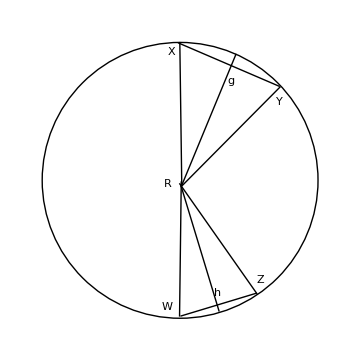

Particle a traverses XY in some time. Meanwhile, Particle b traverses WZ in the same time. Angle XRY=π/4. Angle ZRW=π/6. The radius of the circle, r=2. Point g is at the midpoint of the chord XY. Point h is at the midpoint of the chord WZ.

(a) What are the lengths of Rg and Rh?

(b) What are the lengths of the sagittae going from g to the circumference and from h to the circumference?

(c) What is the ratio of the accelerative force on Particle a to the accelerative force on Particle b?

(d) If Particle a is five times as heavy as Particle b, what is the ratio of the impressed force on Particle a to the impressed force on Particle b?

### 4. Could Newton Have Used Tangents Instead of Chords in Proposition 1 (a riff on an area of investigation suggested by Mishel)

Particle a traverses XY in some time. Meanwhile, Particle b traverses WZ in the same time. Angle XRY=π/4. Angle ZRW=π/6. The radius of the circle, r=2. Point g is at the midpoint of the chord XY. Point h is at the midpoint of the chord WZ.

### 5. Area Under a Curve (much like a problem on the 2nd problem set)

Consider the curve y=e^x/3 in the region x=0 to x=2:

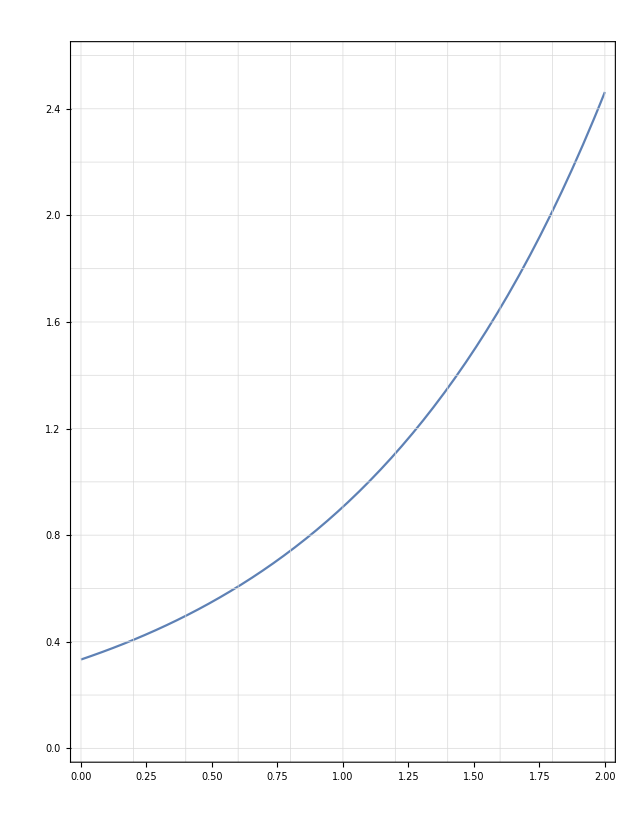

```mathematica
Plot[Exp[x]/3, {x,0, 2}, PlotRange->{{0,2},{0,2.6}}, Ticks->{Range[0, 2, 0.2],Range[0.0, 2.6, 0.2]},GridLines->{Range[0, 2, 0.2],Range[0.0, 2.6, 0.2]}, GridLinesStyle->Medium, Frame->True, AspectRatio->2.6/2]
```

(a) What does each square on the plot represent in terms of area (in other words, what is the product of its width and height)? Count them all up. How many are there? Multiply by the individual area to get the (approximate) total area.

(b) Draw the rectangles that fit under this curve. If you are not sure what I am looking for, the first one to draw is the rectangle going from x=0.0 to x=0.2 that is 1/3 e^0=1/3 high.

(c) Symbolically, the width 0.2 we can write as Δx. So we could have said that the quadrilateral going from x=0.0 to x=0.2, and was 4 high went from x=0Δx=0 to  x=1Δx=Δx and was (1/3 e^0)^2 high. So it is Δx·1/3 e^0 in area. If I say that was the 0th rectangle, and I do the same thing for the other 9 rectangles, and I make k range from 0 to 9, we see that the areas are 1/3 e^kΔx.

So the area is the sum of 1/3 e^kΔx Δx from 0 to 9. Actually, be somewhat more general than that: calculate the sum of 1/3 e^kΔx Δx from 0 to n-1. We know n=10, but instead of plugging that in, leave it as a variable, and also replace Δx by 2/n, since if we divide the range 0 to 2 into n equal parts each of them is 2/n wide.

Your job is to do the sum. I will give you an identity that is easy to prove, and that you need, but you might not know: ∑_(k=0)^(n-1) α^k=(α^n-1)/(α-1)

(d) We made n a variable in part (c) instead of setting it to 10 because the next thing Newton wants us to do is to take the n->∞ limit of what you found. Do that. Discard any terms that disappear in this limit. You will need another approximation to finish:the limit as n-> ∞ of n(e^(2/n)-1) is surprisingly simple. It is just 2.